## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
data=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data,5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

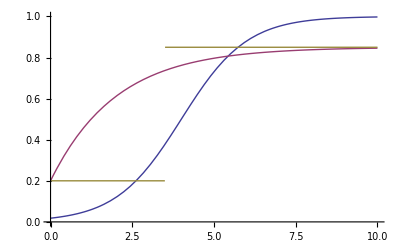

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{l0=Count[Take[data,i],0,1],l1=Count[Take[data,i],1,1],u0=Count[Drop[data,i],0,1],u1=Count[Drop[data,i],1,1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];
	(*Print[{i,g,s,logLike}]; *)If[logLike>best,best=logLike;lBest=i]],{i,0,Length[data]-1}];If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i-1,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0,1]==0 || Count[data,1,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
TableForm[Map[{#[[1]],stepFit[Drop[#,3]]}&,data]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6.
combo-magnification | Null
compo-general-case | 32.9921
compo-general-case-unknown | Null
compo-parallel-axis | 82.3817
compo-perpendicular | 39.1042
compo-z-axis | 16.585
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6.
define-angular-frequency | 9.81909
define-area | Null
define-area-at | Null
define-charge | 28.4934
define-coef-friction | Null
define-compression | Null
define-current-thru | 17.4573
define-distance | 6.
define-distance-between | 9.81909
define-duration | 21.2763
define-electric-power-var | 6.
define-energy-var | Null
define-flux | Null
define-focal-length | 6.
define-frequency | 20.0453
define-grav-accel | 6.
define-image-distance | 8.77259
define-index-of-refraction | 6.
define-magnification | 6.
define-mass | 18.3152
define-mass-density | 6.
define-moment-of-inertia | 6.
define-object-distance | 6.
define-period-var | 8.77259
define-pressure | 15.5607
define-radius-of-circle | 6.
define-resistance-var | 14.9974
define-revolution-radius | 6.
define-shape-length | 6.
define-slit-separation | Null
define-speed | 8.77259
define-spring-constant | 8.77259
define-stored-energy-var | Null
define-turns | Null
define-voltage-across | 23.1989
define-volume | Null
define-wavelength | 6.
define-work | 8.77259
definition-syntax | 6.
draw-accel-free-fall | 6.
draw-accel-slow-down | Null
draw-accel-speed-up | 13.6382
draw-ang-accel | Null
draw-ang-accel-speed-up | Null
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 6.
draw-ang-velocity-rotating | 6.
draw-applied-force | 6.
draw-bfield-straight-current | 8.77259
draw-bforce-charge | 6.
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | 63.6435
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.77259
draw-compo-form-axes | 17.4573
draw-coulomb-force-unknown | 6.
draw-displacement-given-dir | 8.77259
draw-displacement-straight | 10.4987
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 6.
draw-field-given-dir | 9.81909
draw-field-unknown | Null
draw-grav-force | Null
draw-impulse-given-momenta | Null
draw-kinetic-friction | Null
draw-line-given-dir | 13.6382
draw-line-unknown-dir | 6.
draw-momentum-at-rest | Null
draw-momentum-straight | 13.6382
draw-net-field-given-dir | 6.
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | Null
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.4987
draw-point-efield-unknown | Null
draw-projection-axes | 6.
draw-relative-position | 8.77259
draw-relative-position-unknown | 6.
draw-spring-force | Null
draw-tension | 15.5607
draw-torque | Null
draw-unrotated-axes | 25.8748
draw-vector-aligned-axes | 6.
draw-velocity-at-rest | 9.81909
draw-velocity-curved | 14.9974
draw-velocity-curved-unknown | Null
draw-velocity-momentarily-at-rest | 10.4987
draw-velocity-straight | 39.5434
draw-velocity-straight-unknown | Null
draw-weight | 17.1624
draw-xy-vector-given-compos | Null
draw-z-axis-vector-given-compos | Null
equation-syntax | 30.356
equiv-resistance-parallel | 9.81909
equiv-resistance-series | 6.
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 9.81909
magnification-eqn | 6.
object-label | 6.
pendulum-oscillation | Null
pressure-at-open-to-atmosphere | 6.
pressure-force | Null
pressure-height-fluid | Null
sdd-constvel-compo | 9.81909
select-mc-answer | 65.5343
spring-law-compression | Null
spring-mass-oscillation | Null
write-ang-momentum | 6.
write-angle-direction-known-lines | 6.
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | Null
write-capacitance-definition | 6.
write-centripetal-accel | 6.
write-change-me | Null
write-charge-force-bfield | 8.77259
write-charge-force-bfield-mag | Null
write-charge-force-efield-compo | 6.
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | Null
write-cons-angmom | Null
write-cons-linmom-compo-join-split | Null
write-coulomb | Null
write-coulomb-compo | 6.
write-density | Null
write-electric-power | 8.77259
write-energy-cons | 6.
write-equality | 6.
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 6.
write-g-on-earth | Null
write-grav-energy | 11.004
write-harmonic-of | 6.
write-height-dy | Null
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 15.5607
write-known-value-eqn | 235.968
write-linear-vel | Null
write-lk-no-s-compo | 14.3758
write-lk-no-t-compo | Null
write-lk-no-vf-compo | 10.4987
write-loop-rule-capacitors | 11.7416
write-loop-rule-resistors | 10.4987
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 6.
write-net-field-compo | Null
write-net-force-compo | 9.81909
write-nfl-compo | 12.7301
write-nsl-compo | 21.0257
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 17.2868
write-period-circular | Null
write-point-charge-efield-compo | 6.
write-potential-energy | Null
write-right-triangle-tangent | Null
write-rk-no-s | Null
write-rk-no-vf | Null
write-sdd | 8.77259
write-single-loop-rule | Null
write-slit-interference | 6.
write-snells-law | Null
write-spring-energy | 8.77259
write-straight-wire-bfield | Null
write-sum-disp-compo | Null
write-sum-times | Null
write-tensions-equal | 6.
write-total-energy-top | 15.5607
write-transformer-power | Null
write-turns-per-length | Null
write-ug | Null
write-unit-vector-mag | Null
write-vector-magnitude | 6.
write-wave-speed-light | Null
write-wnc | Null
write-work | 6.
wt-law | 17.4573

Add AIC values for all sets with 3 or more points

```mathematica
aics=Apply[Plus,Map[If[Length[Drop[#,3]]≥3,{maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]},0]&,data]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -183.55689551959716`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize will be suppressed during this calculation.

$Aborted

### Generate full table of AIC' s

```mathematica
TableForm[allValues=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]]}&,data]]
```

accel-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

accel-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

accel-constant-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed logistic md5:b50efcf571b671cf01b499841c66daf2

accel-constant-speed bkt md5:b50efcf571b671cf01b499841c66daf2

apply-net-work logistic md5:e66c328693800f93b41f13d97b78e19b

apply-net-work bkt md5:e66c328693800f93b41f13d97b78e19b

apply-net-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

apply-net-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle bkt md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle logistic md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle bkt md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle logistic md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle bkt md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle logistic md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle bkt md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle logistic md5:a38723384afd4471b62218d16045a11d

area-of-circle bkt md5:a38723384afd4471b62218d16045a11d

area-of-circle logistic md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle bkt md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle logistic md5:b50efcf571b671cf01b499841c66daf2

area-of-circle bkt md5:b50efcf571b671cf01b499841c66daf2

bernoulli logistic md5:a38723384afd4471b62218d16045a11d

bernoulli bkt md5:a38723384afd4471b62218d16045a11d

bernoulli logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli logistic md5:55108dec2fb88e9c2af83be92d0520de

bernoulli bkt md5:55108dec2fb88e9c2af83be92d0520de

bernoulli logistic md5:b50efcf571b671cf01b499841c66daf2

bernoulli bkt md5:b50efcf571b671cf01b499841c66daf2

bernoulli logistic md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli bkt md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli logistic md5:e66c328693800f93b41f13d97b78e19b

bernoulli bkt md5:e66c328693800f93b41f13d97b78e19b

bernoulli logistic md5:e3e61859acb08ee896e06e1020f95a49

bernoulli bkt md5:e3e61859acb08ee896e06e1020f95a49

bernoulli logistic md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli bkt md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli logistic md5:8a075e35a0daf7e231f60497d036689a

bernoulli bkt md5:8a075e35a0daf7e231f60497d036689a

combo-magnification logistic md5:a38723384afd4471b62218d16045a11d

combo-magnification bkt md5:a38723384afd4471b62218d16045a11d

combo-magnification logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification logistic md5:b50efcf571b671cf01b499841c66daf2

combo-magnification bkt md5:b50efcf571b671cf01b499841c66daf2

combo-magnification logistic md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification bkt md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification logistic md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification bkt md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification logistic md5:e66c328693800f93b41f13d97b78e19b

combo-magnification bkt md5:e66c328693800f93b41f13d97b78e19b

combo-magnification logistic md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification bkt md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification logistic md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification bkt md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification logistic md5:8a075e35a0daf7e231f60497d036689a

combo-magnification bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case logistic md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case bkt md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case logistic md5:a38723384afd4471b62218d16045a11d

compo-general-case bkt md5:a38723384afd4471b62218d16045a11d

compo-general-case logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case bkt md5:e66c328693800f93b41f13d97b78e19b

compo-general-case logistic md5:8a075e35a0daf7e231f60497d036689a

compo-general-case bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30., -191.898}.

General::stop: Further output of Experimental`NumericalFunction :: nnum will be suppressed during this calculation.

compo-general-case-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis logistic md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis bkt md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis logistic md5:a38723384afd4471b62218d16045a11d

compo-parallel-axis bkt md5:a38723384afd4471b62218d16045a11d

compo-parallel-axis logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-parallel-axis bkt md5:5e8914eb96d8caf02138110b93b5add5

```mathematica
Save["fitAll.m",allValues]
```

### Analyze

Logistic, Baysian Knowledge Tracing, Step model

```mathematica
Get["fitAll.m"];
```

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

```mathematica
allValues[[1]]
```

{accel-at-rest,md5:1da7d76bc3d524d51da47dde26ee8f95,2,6.77259,Null,Null}

```mathematica
cutValues=Select[allValues,#[[3]]≥10&];
```

```mathematica
Length[cutValues]
```

267

```mathematica
Length[Union[Map[First,cutValues]]]
```

38

```mathematica
Length[Union[Map[#[[2]]&,cutValues]]]
```

12

```mathematica
% %%
```

456

```mathematica
aics=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],#[[6]]+aicCorrection[3,#[[3]]]}&,cutValues];
```

```mathematica
akaikeWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,aics];
```

```mathematica
akaikeRawWeights=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,Map[Drop[#,3]&,cutValues]];
```

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights]]
```

{{0.528924,0.502066,0.000698185},{0.112452,0.11831,0.000216223},{0.368088,0.379624,0.000718423}}

```mathematica
Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeRawWeights]]
```

{{0.390206,0.391006,0.000574775},{0.153269,0.148038,0.000241801},{0.466253,0.460956,0.000682496}}

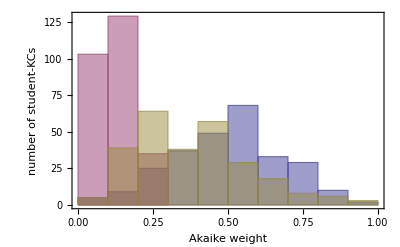
-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step

```mathematica
hc=Histogram[Transpose[akaikeWeights],10,"Count",PlotRange->All,ChartLegends->{"logistic","BKT","step"},Axes->False,Frame->True,FrameLabel->{"Akaike weight","number of student-KCs"}]
```

```mathematica
Overlay[{hc[[1]],hc[[2]]},Alignment->{0.75,0.75}]
```

-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step

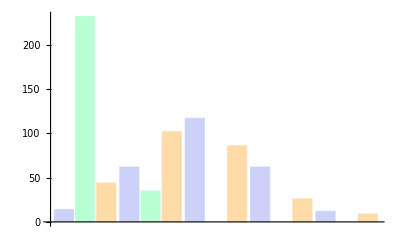
-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step

```mathematica
bc=BarChart[{{14,232,44},{62,35,102},{117,0,86},{62,0,26},{12,0,9}},ChartLegends->Placed[{"logistic","BKT","step"},{{0.5,0.5}}]]
```

```mathematica
Overlay[{bc[[1]],bc[[2]]},Alignment->{0.75,0.75}]
```

-Graphics--Graphics- | logistic
-Graphics- | BKT
-Graphics- | step